```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/neerajsarna/sciebo/DG_MPI/plotting_routines

## Importing data

```mathematica
(*observed error, flag == 0,
 error grid, flag == 1 and 
error velocity flag == 2
num sol flag == 3
adjoint sol == 4*)
importdata[cycle_,flag_,outputdir_]:=Module[{result,filename},
Which[flag == 0,
filename=StringJoin["../",outputdir,"/error_observed_cycle",ToString[cycle],".txt"],
flag == 1,
filename=StringJoin["../",outputdir,"/error_grid_cycle",ToString[cycle],".txt"],

flag == 2,
filename=StringJoin["../",outputdir,"/error_velocity_cycle",ToString[cycle],".txt"],
flag == 3,
filename=StringJoin["../",outputdir,"/result_cycle",ToString[cycle],".txt"],
flag == 4,
filename=StringJoin["../",outputdir,"/resultAdj_cycle",ToString[cycle],".txt"],
flag == 5,
filename=StringJoin["../",outputdir,"/fe_index_cycle",ToString[cycle],".txt"]
];

Print[Style["Reading Data from...",FontColor->Black]];
Print[Style[ToString[filename],FontColor->Green]];
result = Import[filename,"Table"]
]

SortData[data_]:=Module[{indices},
indices = Ordering[data⟦All,1⟧,All,GreaterEqual];
data⟦indices,All⟧
]
```

## Results

```mathematica
M6sol = GetSolutionPoisson[6,0.1,1,bcMBC[6]]⟦3⟧;
M50sol = GetSolutionPoisson[50,0.1,1,bcMBC[50]]⟦3⟧;
```

```mathematica
Clear[errorObs,errorGrid,errorVelocity,resultPrimal,resultAdj,feIndex];
```

```mathematica
Do[
errorObs[cycle]=importdata[cycle,0,"2x1v_moments_wall_Adp"];
errorGrid[cycle]=importdata[cycle,1,"2x1v_moments_wall_Adp"];
errorVelocity[cycle]=importdata[cycle,2,"2x1v_moments_wall_Adp"];
resultPrimal[cycle]=importdata[cycle,3,"2x1v_moments_wall_Adp"];
resultAdj[cycle]=importdata[cycle,4,"2x1v_moments_wall_Adp"];
feIndex[cycle]=importdata[cycle,5,"2x1v_moments_wall_Adp"],{cycle,0,4}];
```

Reading Data from...

../2x1v_moments_wall_Adp/error_observed_cycle0.txt

Reading Data from...

../2x1v_moments_wall_Adp/error_grid_cycle0.txt

Reading Data from...

../2x1v_moments_wall_Adp/error_velocity_cycle0.txt

Reading Data from...

../2x1v_moments_wall_Adp/result_cycle0.txt

Reading Data from...

../2x1v_moments_wall_Adp/result_cycle0.txt

Reading Data from...

../2x1v_moments_wall_Adp/fe_index_cycle0.txt

Reading Data from...

../2x1v_moments_wall_Adp/error_observed_cycle1.txt

Reading Data from...

../2x1v_moments_wall_Adp/error_grid_cycle1.txt

Reading Data from...

../2x1v_moments_wall_Adp/error_velocity_cycle1.txt

Reading Data from...

../2x1v_moments_wall_Adp/result_cycle1.txt

Reading Data from...

../2x1v_moments_wall_Adp/result_cycle1.txt

Reading Data from...

../2x1v_moments_wall_Adp/fe_index_cycle1.txt

Reading Data from...

../2x1v_moments_wall_Adp/error_observed_cycle2.txt

Reading Data from...

../2x1v_moments_wall_Adp/error_grid_cycle2.txt

Reading Data from...

../2x1v_moments_wall_Adp/error_velocity_cycle2.txt

Reading Data from...

../2x1v_moments_wall_Adp/result_cycle2.txt

Reading Data from...

../2x1v_moments_wall_Adp/result_cycle2.txt

Reading Data from...

../2x1v_moments_wall_Adp/fe_index_cycle2.txt

Reading Data from...

../2x1v_moments_wall_Adp/error_observed_cycle3.txt

Reading Data from...

../2x1v_moments_wall_Adp/error_grid_cycle3.txt

Reading Data from...

../2x1v_moments_wall_Adp/error_velocity_cycle3.txt

Reading Data from...

../2x1v_moments_wall_Adp/result_cycle3.txt

Reading Data from...

../2x1v_moments_wall_Adp/result_cycle3.txt

Reading Data from...

../2x1v_moments_wall_Adp/fe_index_cycle3.txt

Reading Data from...

../2x1v_moments_wall_Adp/error_observed_cycle4.txt

Reading Data from...

../2x1v_moments_wall_Adp/error_grid_cycle4.txt

Reading Data from...

../2x1v_moments_wall_Adp/error_velocity_cycle4.txt

Reading Data from...

../2x1v_moments_wall_Adp/result_cycle4.txt

Reading Data from...

../2x1v_moments_wall_Adp/result_cycle4.txt

Reading Data from...

../2x1v_moments_wall_Adp/fe_index_cycle4.txt

```mathematica
Range[1,10]
```

{1,2,3,4,5,6,7,8,9,10}

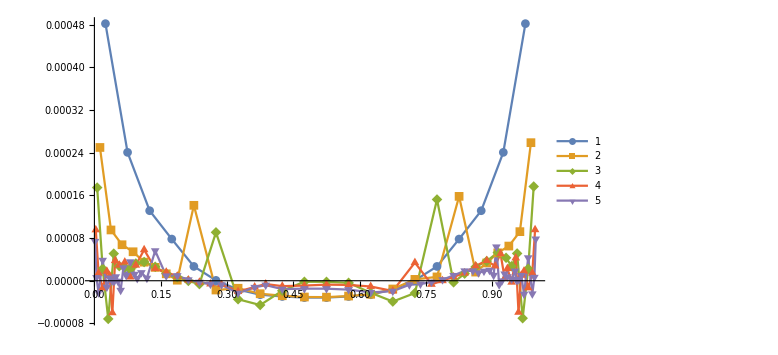

```mathematica
ListPlot[{SortData[errorGrid[0]]⟦All,{1,3}⟧,SortData[errorGrid[1]]⟦All,{1,3}⟧,SortData[errorGrid[2]]⟦All,{1,3}⟧,SortData[errorGrid[3]]⟦All,{1,3}⟧,SortData[errorGrid[4]]⟦All,{1,3}⟧},ImageSize->Large,Joined->True,PlotRange->Full,PlotLegends->Automatic,PlotMarkers->Automatic]
```

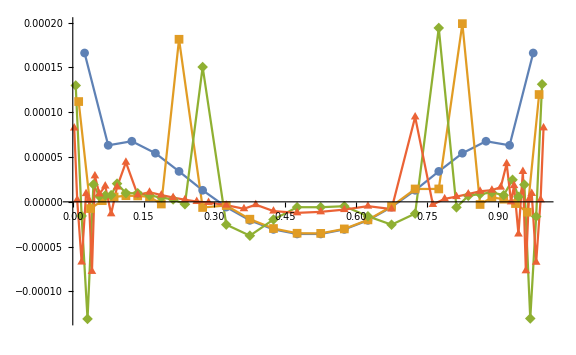

```mathematica
ListPlot[{SortData[errorVelocity[0]]⟦All,{1,3}⟧,SortData[errorVelocity[1]]⟦All,{1,3}⟧,SortData[errorVelocity[2]]⟦All,{1,3}⟧,SortData[errorVelocity[3]]⟦All,{1,3}⟧(*,SortData[errorVelocity[4]]⟦All,{1,3}⟧*)},ImageSize->Large,Joined->True,PlotRange->Full,PlotMarkers->Automatic]
```

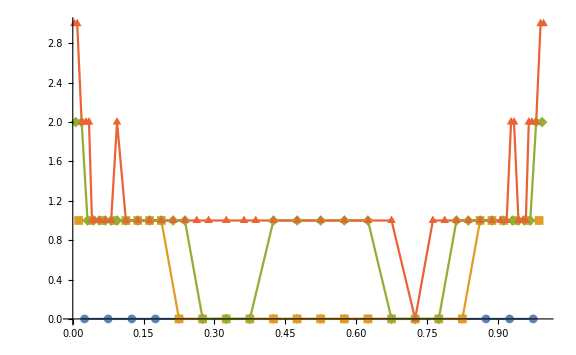

```mathematica
ListPlot[{SortData[feIndex[0]]⟦All,{1,3}⟧,SortData[feIndex[1]]⟦All,{1,3}⟧,SortData[feIndex[2]]⟦All,{1,3}⟧,SortData[feIndex[3]]⟦All,{1,3}⟧(*,SortData[errorVelocity[4]]⟦All,{1,3}⟧*)},ImageSize->Large,Joined->True,PlotRange->Full,PlotMarkers->Automatic]
```

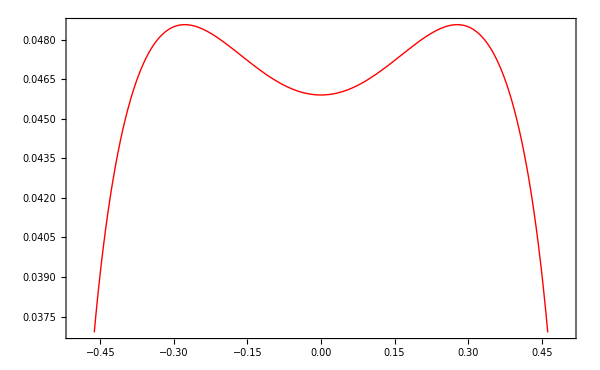

```mathematica
Plot[M50sol,{x,-0.5,0.5}]
```

```mathematica
NIntegrate[M50sol-M6sol,{x,-0.5,0.5}]/0.001153
```

1.26059

```mathematica
convgAdp = Import["../2x1v_moments_wall_Adp/convergence_table_adaptive.txt","Table"];
convgUni = Import["../2x1v_moments_wall_Adp/convergence_table_uniform.txt","Table"];
```

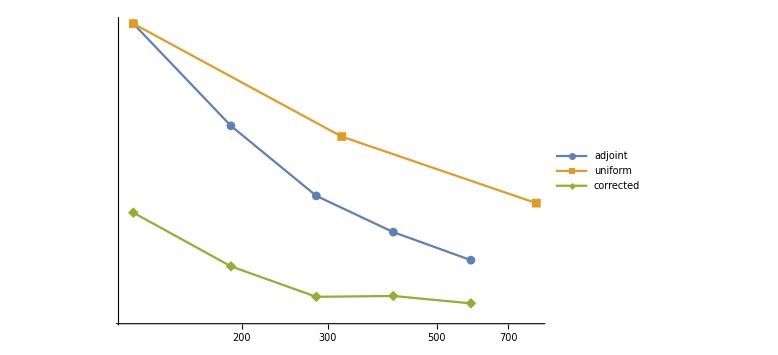

```mathematica
ListLogLogPlot[{convgAdp⟦2;;-1,{6,7}⟧,convgUni⟦2;;-1,{6,7}⟧,convgAdp⟦2;;-1,{6,13}⟧(*,convgAdp⟦2;;-1,{6,9}⟧,convgAdp⟦2;;-1,{6,11}⟧*)},Joined->True,PlotLegends->{"adjoint","uniform","corrected"},PlotMarkers->Automatic,ImageSize->Large,PlotRange->Full]
```

```mathematica
CForm[Chop[Simplify[GetSolutionPoisson[14,0.1,1,bcMBC[14]]⟦3⟧]]]/.{Power->pow,Cosh->cosh}
```

0.05653013082799942 - 0.00003792694823015286*cosh(1.64277980395364*x) - 0.0014402108667994624*cosh(2.0483113377580193*x) - 
   0.00530163981896668*cosh(2.6857066212139475*x) - 0.003996181490901356*cosh(4.230009784703013*x) - 
   0.00006758700357029971*cosh(12.325411809002668*x) + 0.13333333333333333*pow(x,2) - 0.2777777777777778*pow(x,4)

## Validate Grid Refinement

```mathematica
M6sol = GetSolutionPoisson[6,0.1,1,bcMBC[6]]⟦3⟧;
M6adj = GetAdjointPoisson[6,0.1,bcMBC[6]];
```

Solve::svars: Equations may not give solutions for all "solve" variables.

### M6

```mathematica
foldername="2x1v_moments_wall_Adp/validate_grid_error/M6";
```

```mathematica
Do[
errorObs[cycle]=importdata[cycle,0,"2x1v_moments_wall_Adp/validate_grid_error/M6"];
errorGrid[cycle]=importdata[cycle,1,"2x1v_moments_wall_Adp/validate_grid_error/M6"];
resultPrimal[cycle]=importdata[cycle,3,"2x1v_moments_wall_Adp/validate_grid_error/M6"];
resultAdj[cycle]=importdata[cycle,4,"2x1v_moments_wall_Adp/validate_grid_error/M6"];,{cycle,0,3}];
```

Reading Data from...

../2x1v_moments_wall_Adp/validate_grid_error/M6/error_observed_cycle0.txt

Reading Data from...

../2x1v_moments_wall_Adp/validate_grid_error/M6/error_grid_cycle0.txt

Reading Data from...

../2x1v_moments_wall_Adp/validate_grid_error/M6/result_cycle0.txt

Reading Data from...

../2x1v_moments_wall_Adp/validate_grid_error/M6/resultAdj_cycle0.txt

Reading Data from...

../2x1v_moments_wall_Adp/validate_grid_error/M6/error_observed_cycle1.txt

Reading Data from...

../2x1v_moments_wall_Adp/validate_grid_error/M6/error_grid_cycle1.txt

Reading Data from...

../2x1v_moments_wall_Adp/validate_grid_error/M6/result_cycle1.txt

Reading Data from...

../2x1v_moments_wall_Adp/validate_grid_error/M6/resultAdj_cycle1.txt

Reading Data from...

../2x1v_moments_wall_Adp/validate_grid_error/M6/error_observed_cycle2.txt

Reading Data from...

../2x1v_moments_wall_Adp/validate_grid_error/M6/error_grid_cycle2.txt

Reading Data from...

../2x1v_moments_wall_Adp/validate_grid_error/M6/result_cycle2.txt

Reading Data from...

../2x1v_moments_wall_Adp/validate_grid_error/M6/resultAdj_cycle2.txt

Reading Data from...

../2x1v_moments_wall_Adp/validate_grid_error/M6/error_observed_cycle3.txt

Reading Data from...

../2x1v_moments_wall_Adp/validate_grid_error/M6/error_grid_cycle3.txt

Reading Data from...

../2x1v_moments_wall_Adp/validate_grid_error/M6/result_cycle3.txt

Reading Data from...

../2x1v_moments_wall_Adp/validate_grid_error/M6/resultAdj_cycle3.txt

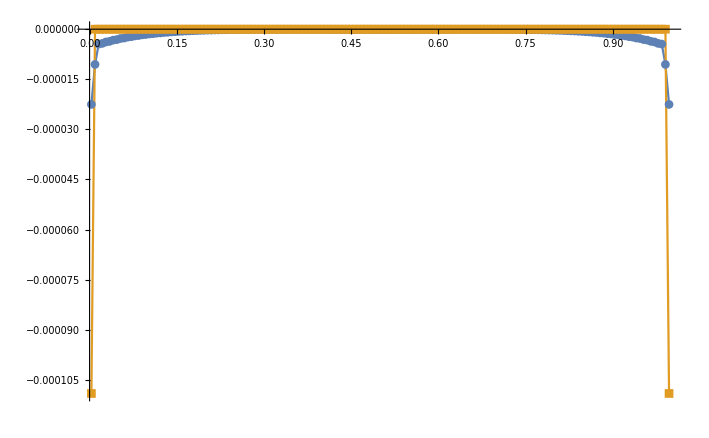

```mathematica
ListPlot[{SortData[errorGrid[3]]⟦All,{1,3}⟧,SortData[errorObs[3]]⟦All,{1,3}⟧},Joined->True,PlotMarkers->Automatic,PlotMarkers->{"o","*"},PlotRange->Full]
```

```mathematica
convgAdp = Import["../2x1v_moments_wall_Adp/validate_grid_error/M6/convergence_table_adaptive.txt","Table"];
convgUni = Import["../2x1v_moments_wall_Adp/validate_grid_error/M6/convergence_table_uniform.txt","Table"];
```

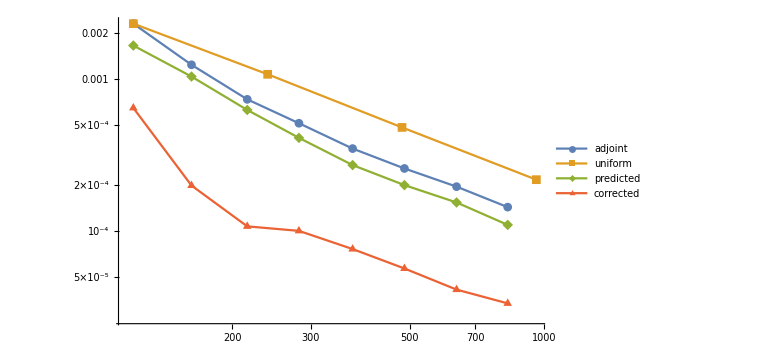

```mathematica
ListLogLogPlot[{convgAdp⟦2;;-1,{6,7}⟧,convgUni⟦2;;-1,{6,7}⟧,convgAdp⟦2;;-1,{6,9}⟧,convgAdp⟦2;;-1,{6,13}⟧},Joined->True,PlotLegends->{"adjoint","uniform","predicted","corrected"},PlotMarkers->Automatic,ImageSize->Large,PlotRange->Full]
```

### 1D wave equation

```mathematica
Do[
errorObs[cycle]=importdata[cycle,0,"1D_wave"];
errorGrid[cycle]=importdata[cycle,1,"1D_wave"];
resultPrimal[cycle]=importdata[cycle,3,"1D_wave"];
resultAdj[cycle]=importdata[cycle,4,"1D_wave"];,{cycle,0,4}];
```

Reading Data from...

../1D_wave/error_observed_cycle0.txt

Reading Data from...

../1D_wave/error_grid_cycle0.txt

Reading Data from...

../1D_wave/result_cycle0.txt

Reading Data from...

../1D_wave/resultAdj_cycle0.txt

Reading Data from...

../1D_wave/error_observed_cycle1.txt

Reading Data from...

../1D_wave/error_grid_cycle1.txt

Reading Data from...

../1D_wave/result_cycle1.txt

Reading Data from...

../1D_wave/resultAdj_cycle1.txt

Reading Data from...

../1D_wave/error_observed_cycle2.txt

Reading Data from...

../1D_wave/error_grid_cycle2.txt

Reading Data from...

../1D_wave/result_cycle2.txt

Reading Data from...

../1D_wave/resultAdj_cycle2.txt

Reading Data from...

../1D_wave/error_observed_cycle3.txt

Reading Data from...

../1D_wave/error_grid_cycle3.txt

Reading Data from...

../1D_wave/result_cycle3.txt

Reading Data from...

../1D_wave/resultAdj_cycle3.txt

Reading Data from...

../1D_wave/error_observed_cycle4.txt

Reading Data from...

../1D_wave/error_grid_cycle4.txt

Reading Data from...

../1D_wave/result_cycle4.txt

Reading Data from...

../1D_wave/resultAdj_cycle4.txt

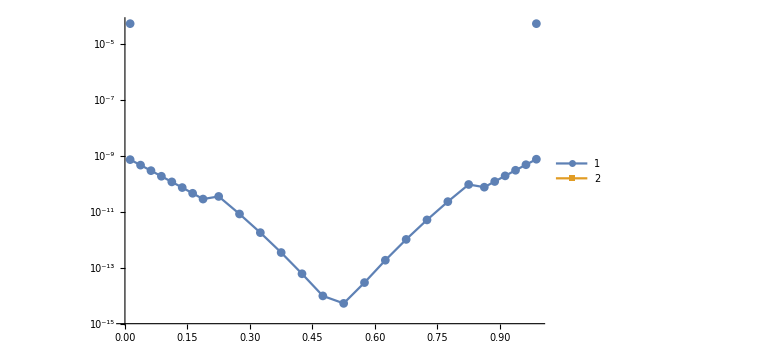

```mathematica
ListLogPlot[{Abs[SortData[errorGrid[1]⟦All,{1,3}⟧]],Abs[SortData[errorObs[1]⟦All,{1,3}⟧]]},PlotLegends->Automatic,PlotRange->Full,Joined->True,ImageSize->Large,PlotMarkers->Automatic]
```

```mathematica
SortData[errorObs[1]⟦All,{1,3}⟧]
```

{{0.9875,0.0000516265},{0.9625,0.},{0.9375,0.},{0.9125,0.},{0.8875,0.},{0.8625,0.},{0.825,0.},{0.775,0.},{0.725,0.},{0.675,0.},{0.625,0.},{0.575,0.},{0.525,0.},{0.475,0.},{0.425,0.},{0.375,0.},{0.325,0.},{0.275,0.},{0.225,0.},{0.1875,0.},{0.1625,0.},{0.1375,0.},{0.1125,0.},{0.0875,0.},{0.0625,0.},{0.0375,0.},{0.0125,-0.0000516305}}

```mathematica
trial = Interpolation[resultPrimal[2]⟦All,{1,3}⟧];
```

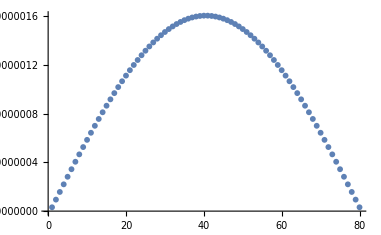

```mathematica
faceLoc = Range[0,1,1/80];
ListPlot[Table[NIntegrate[Sin[π x]-trial[x],{x,faceLoc⟦ii⟧,faceLoc⟦ii+1⟧}],{ii,1,Length[faceLoc]-1}]]
```

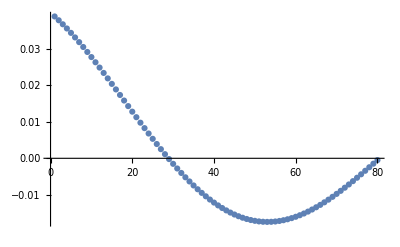

```mathematica
ListPlot[Table[NIntegrate[π Cos[π x](1-x)-trial[x],{x,faceLoc⟦ii⟧,faceLoc⟦ii+1⟧}],{ii,1,Length[faceLoc]-1}]]
```

```mathematica
convgAdp = Import["../1D_wave/convergence_table_adaptive.txt","Table"];
convgUni = Import["../1D_wave/convergence_table_uniform.txt","Table"];
```

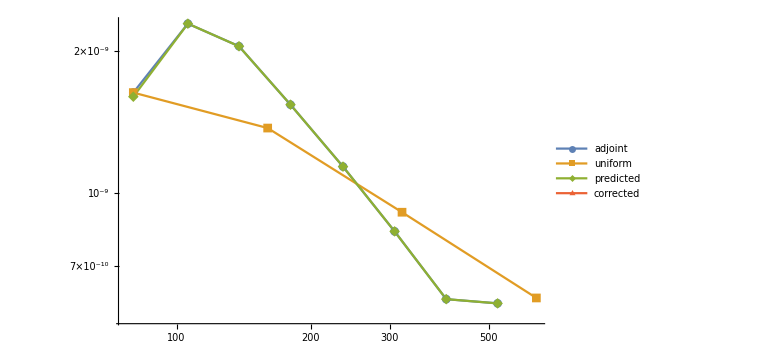

```mathematica
ListLogLogPlot[{convgAdp⟦2;;-1,{6,7}⟧,convgUni⟦2;;-1,{6,7}⟧,convgAdp⟦2;;-1,{6,9}⟧,convgAdp⟦2;;-1,{6,11}⟧},Joined->True,PlotLegends->{"adjoint","uniform","predicted","corrected"},PlotMarkers->Automatic,ImageSize->Large,PlotRange->Full]
```

```mathematica
convgAdp
```

{{primal_error,adjoint_error,min_h,dofs_primal,target_error,predicted_error_grid,predicted_error_velocity,corrected_error},{0.055582,-,0.,-,0.025,80,1.6308×10^-9,-,1.5983×10^-9,-,0.,-,3.2468×10^-11,-},{0.051567,0.27,0.,nan,0.0125,106,2.2829×10^-9,-1.2,2.2829×10^-9,-1.27,0.,nan,3.344×10^-18,57.17},{0.051293,0.02,0.,nan,0.00625,138,2.0445×10^-9,0.42,2.0445×10^-9,0.42,0.,nan,3.7559×10^-17,-9.17},{0.051272,0.,0.,nan,0.003125,180,1.5373×10^-9,1.07,1.5373×10^-9,1.07,0.,nan,2.0992×10^-16,-6.48},{0.051265,0.,0.,nan,0.0015625,236,1.1364×10^-9,1.12,1.1364×10^-9,1.12,0.,nan,5.2259×10^-16,-3.37},{0.051126,0.01,0.,nan,0.00078125,308,8.2848×10^-10,1.19,8.2848×10^-10,1.19,0.,nan,4.2811×10^-16,0.75},{0.050723,0.03,0.,nan,0.00078125,402,5.952×10^-10,1.24,5.952×10^-10,1.24,0.,nan,4.1572×10^-16,0.11},{0.049783,0.07,0.,nan,0.00039062,524,5.8306×10^-10,0.08,5.8306×10^-10,0.08,0.,nan,2.8287×10^-16,1.45}}

### manufactured M = 4

```mathematica
foldername = "2x1v_moments_wall_Adp/validate_grid_error/M6/";
Do[
errorObs[cycle]=importdata[cycle,0,foldername];
errorGrid[cycle]=importdata[cycle,1,foldername];
resultPrimal[cycle]=importdata[cycle,3,foldername];
resultAdj[cycle]=importdata[cycle,4,foldername];,{cycle,0,2}];
```

Reading Data from...

../2x1v_moments_wall_Adp/validate_grid_error/M6//error_observed_cycle0.txt

Reading Data from...

../2x1v_moments_wall_Adp/validate_grid_error/M6//error_grid_cycle0.txt

Reading Data from...

../2x1v_moments_wall_Adp/validate_grid_error/M6//result_cycle0.txt

Reading Data from...

../2x1v_moments_wall_Adp/validate_grid_error/M6//resultAdj_cycle0.txt

Reading Data from...

../2x1v_moments_wall_Adp/validate_grid_error/M6//error_observed_cycle1.txt

Reading Data from...

../2x1v_moments_wall_Adp/validate_grid_error/M6//error_grid_cycle1.txt

Reading Data from...

../2x1v_moments_wall_Adp/validate_grid_error/M6//result_cycle1.txt

Reading Data from...

../2x1v_moments_wall_Adp/validate_grid_error/M6//resultAdj_cycle1.txt

Reading Data from...

../2x1v_moments_wall_Adp/validate_grid_error/M6//error_observed_cycle2.txt

Reading Data from...

../2x1v_moments_wall_Adp/validate_grid_error/M6//error_grid_cycle2.txt

Reading Data from...

../2x1v_moments_wall_Adp/validate_grid_error/M6//result_cycle2.txt

Reading Data from...

../2x1v_moments_wall_Adp/validate_grid_error/M6//resultAdj_cycle2.txt

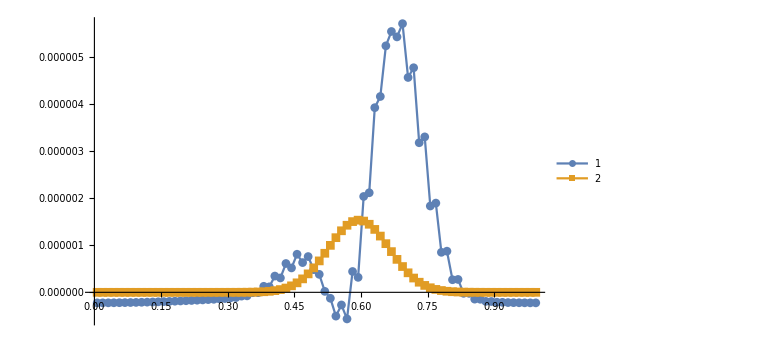

```mathematica
ListPlot[{errorGrid[2]⟦All,{1,3}⟧,errorObs[2]⟦All,{1,3}⟧},PlotLegends->Automatic,PlotRange->Full,Joined->True,ImageSize->Large,PlotMarkers->Automatic]
```

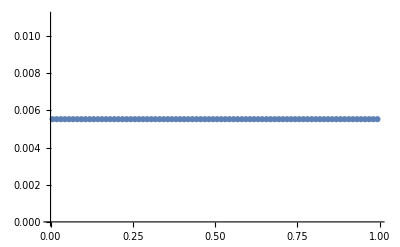

```mathematica
ListPlot[{resultAdj[2]⟦All,{1,4}⟧},PlotRange->Full]
```

```mathematica
trial = Interpolation[resultPrimal[2]⟦All,{1,4}⟧];
```

InterpolatingFunction::dmval: Input value {0.0000204286} lies outside the range of data in the interpolating function. Extrapolation will be used.

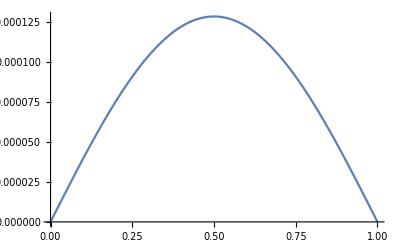

```mathematica
Plot[{Sin[π x]-trial[x]},{x,0,1}]
```